### Perturbation matrix for lattice in 2 site case

```mathematica
SetDirectory[NotebookDirectory[]];
kinetic = Import["211_t.dat"];
Length[kinetic]
Table[ kinetic[[i,j]]t,{i,1,Length[kinetic]},{j,1,Length[kinetic]}]
```

4

{{0.,-1. t,-1. t,0.},{-1. t,0.,0.,-1. t},{-1. t,0.,0.,-1. t},{0.,-1. t,-1. t,0.}}

```mathematica
interaction =  Import["211_U.dat"];
energy =kinetic+interaction;
MatrixForm[energy]
MatrixForm[Transpose[Eigenvectors[energy]]]
MatrixForm[Eigenvalues[energy]]
```

(0.+1. U | 0.-1. t | 0.-1. t | 0.
0.-1. t | 0. | 0. | 0.-1. t
0.-1. t | 0. | 0. | 0.-1. t
0. | 0.-1. t | 0.-1. t | 0.+1. U)

(0. | -(-2. t^3 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1]-1. t U Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1]^2+1. t Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1]^3)/((0.-1. t) (0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1])) | -(-2. t^3 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2]-1. t U Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2]^2+1. t Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2]^3)/((0.-1. t) (0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2])) | -(-2. t^3 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3]-1. t U Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3]^2+1. t Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3]^3)/((0.-1. t) (0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3]))
-1. | -(0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1])/(0.-1. t)-((0.+(0.-1. t) (0.-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1])) (0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1]))/(0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1]) | -(0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2])/(0.-1. t)-((0.+(0.-1. t) (0.-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2])) (0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2]))/(0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2]) | -(0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3])/(0.-1. t)-((0.+(0.-1. t) (0.-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3])) (0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3]))/(0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3])
1. | (1. (0.+(0.-1. t) (0.-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1])) (0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1]))/(0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1]) | (1. (0.+(0.-1. t) (0.-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2])) (0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2]))/(0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2]) | (1. (0.+(0.-1. t) (0.-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3])) (0.+1. U-1. Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3]))/(0.+2. t^2 Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3])
0. | 1. | 1. | 1.)

(0
Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,1]
Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,2]
Root[4. t^2 U+(-4. t^2+1. U^2) #1-2. U #1^2+1. #1^3&,3])

### Exact analytical diagonalization of 2 site Fermi-Hubbard model at half filling.

```mathematica
mlatt={{U,0,-t,-t},{0,U,-t,-t},{-t,-t,0,0},{-t,-t,0,0}};
MatrixForm[mlatt]
MatrixForm[Transpose[Eigenvectors[mlatt]]]
e=Eigenvalues[mlatt]
MatrixForm[e]
```

(U | 0 | -t | -t
0 | U | -t | -t
-t | -t | 0 | 0
-t | -t | 0 | 0)

(0 | -1 | (4 t)/(U+√(16 t^2+U^2)) | -(4 t)/(-U+√(16 t^2+U^2))
0 | 1 | (4 t)/(U+√(16 t^2+U^2)) | -(4 t)/(-U+√(16 t^2+U^2))
-1 | 0 | 1 | 1
1 | 0 | 1 | 1)

{0,U,1/2 (U-√(16 t^2+U^2)),1/2 (U+√(16 t^2+U^2))}

(0
U
1/2 (U-√(16 t^2+U^2))
1/2 (U+√(16 t^2+U^2)))

```mathematica
mlatt={{U,-t,-t,0},{-t,0,0,-t},{-t,0,0,-t},{0,-t,-t,U}};
MatrixForm[mlatt]
MatrixForm[Transpose[Eigenvectors[mlatt]]]
e=Eigenvalues[mlatt]
MatrixForm[e]
```

(U | -t | -t | 0
-t | 0 | 0 | -t
-t | 0 | 0 | -t
0 | -t | -t | U)

(0 | -1 | 1 | 1
-1 | 0 | U/(4 t)+(√(16 t^2+U^2))/(4 t) | -(-U+√(16 t^2+U^2))/(4 t)
1 | 0 | -(-U-√(16 t^2+U^2))/(4 t) | -(-U+√(16 t^2+U^2))/(4 t)
0 | 1 | 1 | 1)

{0,U,1/2 (U-√(16 t^2+U^2)),1/2 (U+√(16 t^2+U^2))}

(0
U
1/2 (U-√(16 t^2+U^2))
1/2 (U+√(16 t^2+U^2)))

#### In the limit of large U/t the term in the square root goes to U + 8*t^2/U

{0,U,1/2 (U-√(16 t^2+U^2)),1/2 (U+√(16 t^2+U^2))}

(0
U
1/2 (U-√(16 t^2+U^2))
1/2 (U+√(16 t^2+U^2)))

```mathematica
Assuming[U>0 ,Series[e[[3]],{t,0,2}]]
Assuming[U>0 ,Series[e[[4]],{t,0,2}]]
```

### Make some plot of the eigenvalues and eigenvectors as a function of x=U/t

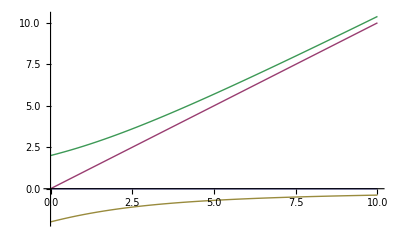

```mathematica
Plot[{0,x,1/2(x-√(16+x^2)),1/2(x+√(16+x^2))},{x,0,10}]
```

### Perturbation matrix for lattice + interactions

```mathematica
mint={{E0+U,0,t,t},{0,E0+U,t,t},{t,t,E0,0},{t,t,0,E0}};
MatrixForm[mint]
```

(E0+U | 0 | t | t
0 | E0+U | t | t
t | t | E0 | 0
t | t | 0 | E0)

```mathematica
MatrixForm[Transpose[Eigenvectors[mint]]]
MatrixForm[Eigenvalues[mint]]
```

(0 | -1 | -(4 t)/(U+√(16 t^2+U^2)) | (4 t)/(-U+√(16 t^2+U^2))
0 | 1 | -(4 t)/(U+√(16 t^2+U^2)) | (4 t)/(-U+√(16 t^2+U^2))
-1 | 0 | 1 | 1
1 | 0 | 1 | 1)

(E0
E0+U
1/2 (2 E0+U-√(16 t^2+U^2))
1/2 (2 E0+U+√(16 t^2+U^2)))